```mathematica
%%%Ref. 1: T. Schoenenbach, et al, MNRAS 430 (2013), 2999-3009%%%
```

```mathematica
%%%Calculation is restricted to the orbital plane \theta=pi/2
%%% Massunit m=1-> r is in units of m
```

```mathematica
theta=Pi/2
m:=1
```

π/2

```mathematica
%%%For the definition of Sigma, Psi, Delta and the metric see Ref. 1%%%
```

```mathematica
Sigma[r_,a_,theta_]:=r^2 +a^2 Cos[theta]^2
Psi[r_,B_,m_]:= 2*m*r - B/(2*r)
Delta[r_,a_,B_,m_]:= r^2 +a^2 - Psi[r,B,m]
```

```mathematica
g00[r_,a_,B_,m_,theta_]:=-(1 - Psi[r,B,m]/Sigma[r,a,theta])
g11[r_,a_,B_,m_,theta_]:=Sigma[r,a,theta]/Delta[r,a,B,m]
g22[r_,a_,theta_]:=Sigma[r,a,theta]
g33[r_,a_,B_,m_,theta_]:=(r^2+a^2+ (a^2Psi[r,B,m])/Sigma[r,a,theta]*Sin[theta]^2)Sin[theta]^2
g03[r_,a_,B_,m_,theta_]:=-a Psi[r,B,m]/Sigma[r,a,theta]*Sin[theta]^2
```

```mathematica
%%%definition of then function h(r), see Ref. 1, also for omegapro (pro=prograde)
%%% Domegapro=derivative of omegaprp with respect to r
```

```mathematica
hauxiliary[r_,B_,m_]:=2*m/r^2  -(3 B)/(2r^4)
omegapro[r_,a_,B_,m_]:=1/(a+ Sqrt[2*r/(hauxiliary[r,B,m])])
omegaretro[r_,a_,B_,m_]:=1/(a- Sqrt[2*r/(hauxiliary[r,B,m])])
```

```mathematica
Domegapro[r_,a_,B_,m_]:=D[1/(a+ Sqrt[2*x/(hauxiliary[x,B,m])]),x]/.x->r
```

```mathematica
%%%Derivatives of the metric components with respect to r
```

```mathematica
dg00[r_,a_,B_,m_,theta_]:=D[g00[r,a,B,m,theta],r]
ddg00[r_,a_,B_,m_,theta_]:=D[dg00[r,a,B,m,theta],r]
```

```mathematica
dg33[r_,a_,B_,m_,theta_]:=D[g33[r,a,B,m,theta],r]
ddg33[r_,a_,B_,m_,theta_]:=D[dg33[r,a,B,m,theta],r]
```

```mathematica
dg03[r_,a_,B_,m_,theta_]:=D[g03[r,a,B,m,theta],r]
ddg03[r_,a_,B_,m_,theta_]:=D[dg03[r,a,B,m,theta],r]
```

```mathematica
%%%Function Delta (see Ref. 1) and its derivatives in r
```

```mathematica
Delt[r_,a_,B_,m_]:= r^2 +a^2 - Psi[r,B,m]
dDelt[r_,a_,B_,m_]:=D[Delt[r,a,B,m],r]
ddDelt[r_,a_,B_,m_]:=D[dDelt[r,a,B,m],r]
```

```mathematica
%%%Choose b(here the letter B is used), B=0: GR, B=64/27 fot n=3
```

```mathematica
B=0
```

0

```mathematica
%%%FFa=0 is the equation for the last stable orbit in GR, needed later
```

```mathematica
FFa[r_,a_,B_]:=ddg33[r,a,B,m,theta](g00[r,a,B,m,theta]+omegapro[r,a,B,m]g03[r,a,B,m,theta])^2+ddg00[r,a,B,m,theta](g03[r,a,B,m,theta]+omegapro[r,a,B,m]g33[r,a,B,m,theta])^2 - 2 ddg03[r,a,B,m,theta](g00[r,a,B,m,theta]+omegapro[r,a,B,m]g03[r,a,B,m,theta])(g03[r,a,B,m,theta]+omegapro[r,a,B,m]g33[r,a,B,m,theta])+ddDelt[r,a,B,m](omegapro[r,a,B,m]^2 g33[r,a,B,m,theta]+ 2 omegapro[r,a,B,m]g03[r,a,B,m,theta]+ g00[r,a,B,m,theta])
```

```mathematica
Simplify[FFa[r,a,B]]
```

-(2 (-3 a^2 r+(-6+r) r^2+8 a √(r^3)))/(r (a+√(r^3))^2)

```mathematica
%%%Only the numerator is important for solving the equation FFa=0
```

```mathematica
FFb[r,a]=2 (-3 a^2 r+(-6+r) r^2+8 a √(r^3))
```

2 (-3 a^2 r+(-6+r) r^2+8 a √(r^3))

```mathematica
%%% Now comes pc-GR
```

```mathematica
B=64/27
```

64/27

```mathematica
%%%GGa =0 gives the equation for the stable orbit (see Ref. 1, Equ. (41))
```

```mathematica
GGa[r_,a_,B_]:=ddg33[r,a,B,m,theta](g00[r,a,B,m,theta]+omegapro[r,a,B,m]g03[r,a,B,m,theta])^2+ddg00[r,a,B,m,theta](g03[r,a,B,m,theta]+omegapro[r,a,B,m]g33[r,a,B,m,theta])^2 - 2 ddg03[r,a,B,m,theta](g00[r,a,B,m,theta]+omegapro[r,a,B,m]g03[r,a,B,m,theta])(g03[r,a,B,m,theta]+omegapro[r,a,B,m]g33[r,a,B,m,theta])+ddDelt[r,a,B,m](omegapro[r,a,B,m]^2 g33[r,a,B,m,theta]+ 2 omegapro[r,a,B,m]g03[r,a,B,m,theta]+ g00[r,a,B,m,theta])
```

```mathematica
Simplify[GGa[r,a,B]]
```

-((2 (2160 a^2 r^3+(432-729 a^2) r^5-1458 r^6+243 r^7+18432 a √(r^5/(-16+9 r^2))-256 r^2 (10+81 a √(r^5/(-16+9 r^2)))+72 r^4 (40+81 a √(r^5/(-16+9 r^2)))))/(27 r^3 (-16+9 r^2) (a+3 √(r^5/(-16+9 r^2)))^2))

```mathematica
%%%Only the numerator is important to fin d the zeros (we have multiplied by the denominator of GGa)
```

```mathematica
GGb[r_,a_]=(2 (2160 a^2 r^3+(432-729 a^2) r^5-1458 r^6+243 r^7+18432 a √(r^5/(-16+9 r^2))-256 r^2 (10+81 a √(r^5/(-16+9 r^2)))+72 r^4 (40+81 a √(r^5/(-16+9 r^2)))))
```

2 (2160 a^2 r^3+(432-729 a^2) r^5-1458 r^6+243 r^7+18432 a √(r^5/(-16+9 r^2))-256 r^2 (10+81 a √(r^5/(-16+9 r^2)))+72 r^4 (40+81 a √(r^5/(-16+9 r^2))))

```mathematica
%%%Plot of the last stable orbot in GR
```

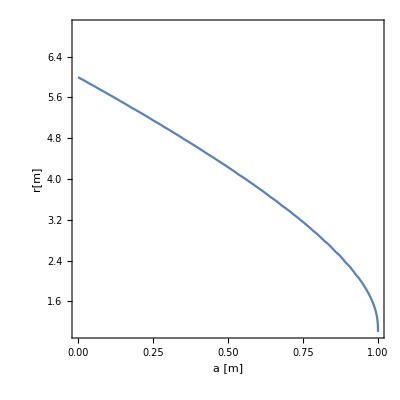

```mathematica
ContourPlot[FFb[r,a]==0,{a,0,1},{r,1,7},FrameTicksStyle-> Directive[Blue,14],FrameLabel-> {"a [m]","r[m]"}]
```

```mathematica
%%%Plot of the last stable orbot in pc-GR
```

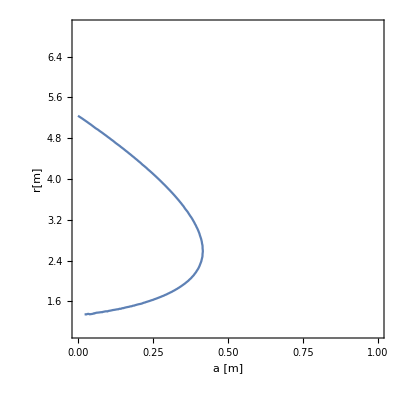

```mathematica
ContourPlot[GGb[r,a]==0,{a,0,1},{r,1,7},FrameTicksStyle-> Directive[Blue,14],FrameLabel-> {"a [m]","r[m]"}]
```

```mathematica
%%%joining the last two plots. (%4... numbers  MAY HAVE TO BE CHANGED)
```

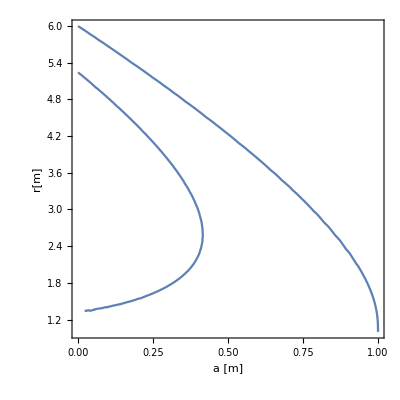

```mathematica
Show[%34,%33,PlotRange->All]
```